```mathematica
ODE = 2/ζ θ'[ζ]+θ''[ζ]+θ[ζ]== 0;
```

```mathematica
AsymptoticDSolveValue[{ODE},θ,{ζ,0,5}];
```

```mathematica
(1-ζ^2/6+ζ^4/120) C[1]+(1/ζ-ζ/2+ζ^3/24) C[2]
```

(1-ζ^2/6+ζ^4/120) C[1]+(1/ζ-ζ/2+ζ^3/24) C[2]

Since second solution diverges, physical solution is C[1]

```mathematica
1-ζ^2/6+ζ^4/120
```

1-ζ^2/6+ζ^4/120

Hence Other initial Condition is θ’[0]=0

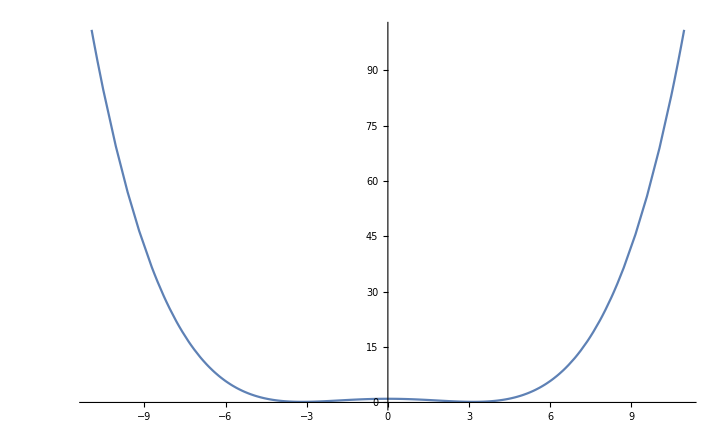

```mathematica
Plot[1-ζ^2/6+ζ^4/120,{ζ,-10.954451150103322,10.954451150103322}]
```

```mathematica
DSolve[{ODE, θ[0]==1,θ'[0]==0},θ,{ζ}]
```

{{θ→Function[{ζ},-(ⅈ ⅇ^(-ⅈ ζ) (-1+ⅇ^(2 ⅈ ζ)))/(2 ζ)]}}

```mathematica
{{θ->Function[{ζ},-(ⅈ ⅇ^(-ⅈ ζ) (-1+ⅇ^(2 ⅈ ζ)))/(2 ζ)]}}⟦1,1,2⟧
```

Function[{ζ},-(ⅈ ⅇ^(-ⅈ ζ) (-1+ⅇ^(2 ⅈ ζ)))/(2 ζ)]

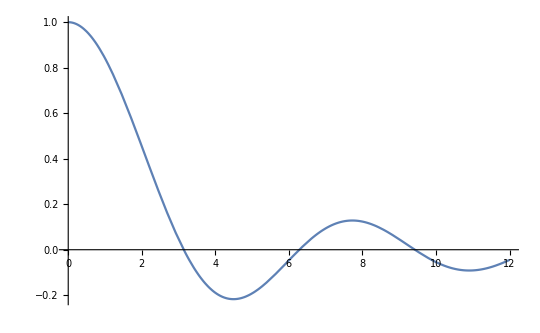

```mathematica
Plot[Function[{ζ},-(ⅈ ⅇ^(-ⅈ ζ) (-1+ⅇ^(2 ⅈ ζ)))/(2 ζ)][x],{x,0,12.}]
```

```mathematica
Show[%10,AxesLabel->{HoldForm[ξ],HoldForm[θ]},PlotLabel->HoldForm[Solution for n=1 Lane-Emden],LabelStyle->{GrayLevel[0]}]
```

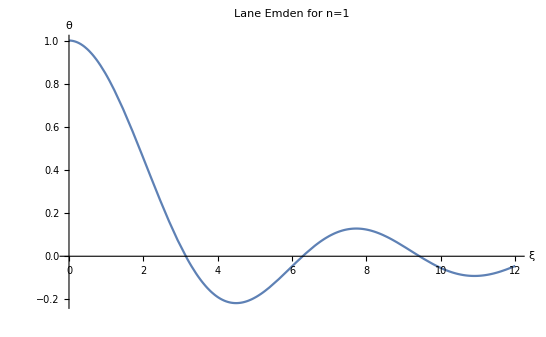

```mathematica
Show[%11,PlotLabel->HoldForm[Lane Emden for n=1]]
```